# Functions for testing d2E/dgamma^2and dE/dgamma

## Analytical functions

```mathematica
(*Cross product for 2d vectors*)
Cross2d[r1_,r2_]:=r1[[1]]r2[[2]]-r1[[2]]r2[[1]]
(*The vertex position given the three adjecent cell positions*)
voro[ri_,rj_,rk_]:=Module[{rij,rjk,rik,cross,d,α,β,γ},
rij=ri-rj;
rjk=rj-rk;
rik=ri-rk;

cross=Cross2d[rij,rjk];
d=2*cross*cross;

α=(rjk.rjk)*(rij.rik)/d;
β=-(rik.rik)*(rij.rjk)/d;
γ=(rij.rij)*(rik.rjk)/d;

α*ri+β*rj+γ*rk
];
```

```mathematica
(*calculate perimetes and areas given the positions of all the vertices*)
peri[hv_List]:=Sum[Sqrt[(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]).(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]])],{i,1,Length[hv]}];

area[hv_List]:=Sum[0.5*Cross2d[hv[[i]],hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]],{i,1,Length[hv]}];
```

```mathematica
(*This is the 1st derivative of e w.r.t. h*)
dedhGeneral[hv_List,KA_,KP_,PA_,PP_]:=Module[{dedhx,dedhy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
dedhx=(-1. hiLasty+1. hiNexty) KA (a-PA)+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
dedhy=(-1. hiLastx+1. hiNextx) KA (PA-a)+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
{dedhx,dedhy}
]
```

```mathematica
(*This is the generalized function for de2dhidhj*)

de2dhihjxx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xx=2 ((-0.5 hiLasty+0.5 hiNexty)^2 KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLastx+hix)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNextx+hix)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2xx=2 ((-0.5 hiy+0.5 hjNexty) (-0.5 hiLasty+0.5 hjy) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[j==Length[hv],
de2xx=2 ((0.5 hiy-0.5 hjLasty) (0.5 hiNexty-0.5 hjy) KA+((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2xx=2 (-0.5 hiLasty+0.5 hiNexty) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xx
];
de2dhihjxy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xy=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2xy=2 (0.5 hix-0.5 hjNextx) (-0.5 hiLasty+0.5 hjy) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP- KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2xy=2 (-0.5 hix+0.5 hjLastx) (0.5 hiNexty-0.5 hjy) KA+2 ((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP+KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2xy=2 (-0.5 hiLasty+0.5 hiNexty) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xy
];
de2dhihjyx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yx=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2yx=2 (-0.5 hiy+0.5 hjNexty) (0.5 hiLastx-0.5 hjx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP+ KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2yx=2 (0.5 hiy-0.5 hjLasty) (-0.5 hiNextx+0.5 hjx) KA+2 ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) ((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) KP-KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2yx=2 (0.5 hiLastx-0.5 hiNextx) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yx
];
de2dhihjyy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yy=2 ((-0.5 hiLastx+0.5 hiNextx)^2 KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLasty+hiy)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNexty+hiy)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2yy=2 ((0.5 hix-0.5 hjNextx) (0.5 hiLastx-0.5 hjx) KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[j==Length[hv],
de2yy=2 ((-0.5 hix+0.5 hjLastx) (-0.5 hiNextx+0.5 hjx) KA+((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2yy=2 (0.5 hiLastx-0.5 hiNextx) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yy
];
de2dhdhGeneral[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{},
{{de2dhihjxx[hv,j,KA,KP,PA,PP],de2dhihjxy[hv,j,KA,KP,PA,PP]},{de2dhihjyx[hv,j,KA,KP,PA,PP],de2dhihjyy[hv,j,KA,KP,PA,PP]}}
]
```

```mathematica
(*These are the analytical forms for dhdgamma and d2hdgamma2*)
dhdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{(r1x r1y (r2y-r3y)+r2y (r2x-r3x) r3y+r1y (-r2x r2y+r3x r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-2 r2x r2y r3x+r2y r3x^2-r2x^2 r3y-r2y^2 r3y+2 r2x r3x r3y+r2y r3y^2+r1x^2 (-r2y+r3y)+r1y^2 (-r2y+r3y)+2 r1x (r2x r2y+r1y (-r2x+r3x)-r3x r3y)+r1y (r2x^2+r2y^2-r3x^2-r3y^2))/(2 (-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y))}
];
d2hdgdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{((r1y-r2y) (r1y-r3y) (r2y-r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-r2y^2 r3x+r1y^2 (-r2x+r3x)-2 r2x r2y r3y+2 r2y r3x r3y+r2x r3y^2+r1x (r2y^2-r3y^2)+2 r1y (r2x r2y-r3x r3y+r1x (-r2y+r3y)))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y)}
];
```

```mathematica
(*Now this is to calculate de2dgammadgamma for cell i*)
d2eidgdgGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[Sum[de2dhdhGeneral[RotateLeft[vList,i],j,KA,KP,PA,PP].dhdgGeneral[ri,allPoints[[neilist[[If[j+i==Length[vList],Length[vList],Mod[j+i,Length[vList]]]]]]],allPoints[[neilist[[If[j+1+i==Length[vList]||j+1+i==2*Length[vList],Length[vList],Mod[j+1+i,Length[vList]]]]]]]].dhdgGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{j,1,Length[vList]}]+dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].d2hdgdgGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
]
```

```mathematica
(*Now this is to calculate dedgamma for cell i*)
deidgGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].dhdgGeneral[ri,allPoints[[neilist[[If[i+1==Length[vList],Length[vList],Mod[i+1,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList]||2+i==2*Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
]
```

```mathematica
(*This gives the neighbor list of cell i in a counterclock-wise order and this neighbor list aligns with the vertex id list*)
```

```mathematica
reorderCCWIndices[centerIndex_,neighborIndices_List,allPoints_]:=Module[{center,neighbors,angles,sortedIndices},center=allPoints[[centerIndex]];
neighbors=allPoints[[neighborIndices]];
angles=ArcTan@@@(#-center&/@neighbors);
sortedIndices=Ordering[angles];
neighborIndices[[sortedIndices]]
(*Table[neighborIndices[[FirstPosition[sortedIndices,i][[1]]]],{i,1,Length[neighborIndices]}]*)];
neighborListRightOrder[i_,voronoiPolygons_List,cellIndex_,allPoints_]:=Module[{trianglesWithCenteri,neighborListRandomOrder,neighborListCCWOrder,delaunay,vetices,firstVerticeID},
delaunay=DelaunayMesh[allPoints];
trianglesWithCenteri=Select[First/@MeshCells[delaunay,2],MemberQ[#,i]&];
neighborListRandomOrder=DeleteCases[Union[Flatten[trianglesWithCenteri]],i];
neighborListCCWOrder=reorderCCWIndices[i,neighborListRandomOrder,allPoints];
vetices=Table[voro[allPoints[[i]],allPoints[[neighborListCCWOrder[[j]]]],allPoints[[neighborListCCWOrder[[If[j+1==Length[neighborListCCWOrder],Length[neighborListCCWOrder],Mod[j+1,Length[neighborListCCWOrder]]]]]]]],{j,1,Length[neighborListCCWOrder]}];
firstVerticeID=Nearest[vetices->Automatic,voronoiPolygons[[cellIndex[[i]]]][[1]][[1]]][[1]];
RotateLeft[neighborListCCWOrder,firstVerticeID-1]
];
```

```mathematica
(*This is the function that returns a list of dei/dg and d2ei/dg2 for each cell*)
AnalyticalCell[allPoints_,box_List,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Table[{deidgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidgdgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
```

```mathematica
AnalyticalCellTest[allPoints_,box_List,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Table[{deidgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidgdgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
```

## Numerical function:

```mathematica
getData[fname_]:=Module[{t,n,frames,types,times,positions,posSet},
t=Import[fname,"Data"];
n=Length[t[[8,1]]]/2;
frames=Length[t[[2]]];
times=Flatten[t[[2]]];
positions={};
Do[
posSet=t[[8,fr]];
AppendTo[positions,Table[{posSet[[2*i+1]],posSet[[2*i+2]]},{i,0,n-1}]];
,{fr,1,frames}];
{n,frames,positions,types,times}];
```

```mathematica
(*This function returns dei/dg and d2ei/dg^2 for each cell*)
```

```mathematica
numdericalCell[allPoints_List,box_List,ddx_,ka_,kp_,pa_,pp_]:=Module[{Vareas0,Vperis0,Vareas1,Vperis1,VareasI,VperisI,copies,translations,translatedCopies,allPointsPBD,cellIndex,cellIndex0,cellIndex1,strainfor,strainback,vm,vm1,vm0,allPointsPBD0,allPointsPBD1,min,max,voronoiPolygons,voronoiPolygons1,voronoiPolygons0},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
strainfor={{1,ddx},{0,1}};
strainback={{1,-ddx},{0,1}};
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD0=strainfor.#&/@allPointsPBD;
vm0=VoronoiMesh[allPointsPBD0,{{min,max},{min,max}}];
voronoiPolygons0=MeshPrimitives[vm0,2];
cellIndex0=Table[Position[Table[RegionMember[voronoiPolygons0[[j]],allPointsPBD0[[i]]],{j,Length[allPointsPBD0]}],True][[1,1]],{i,Length[allPoints]}];
Vareas0=PropertyValue[{vm0,2},MeshCellMeasure];
Vperis0=RegionMeasure/@(MeshPrimitives[vm0,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD1=strainback.#&/@allPointsPBD;
vm1=VoronoiMesh[allPointsPBD1,{{min+0.001*min,max+0.001*max},{min,max}}];
Vareas1=PropertyValue[{vm1,2},MeshCellMeasure];
Vperis1=RegionMeasure/@(MeshPrimitives[vm1,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
voronoiPolygons1=MeshPrimitives[vm1,2];
cellIndex1=Table[Position[Table[RegionMember[voronoiPolygons1[[j]],allPointsPBD1[[i]]],{j,Length[allPointsPBD1]}],True][[1,1]],{i,Length[allPoints]}];
Table[{(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2-ka(Vareas1[[cellIndex1[[i]]]]-pa)^2-kp(Vperis1[[cellIndex1[[i]]]]-pp)^2)/(2*ddx),(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2+ka(Vareas1[[cellIndex1[[i]]]]-pa)^2+kp(Vperis1[[cellIndex1[[i]]]]-pp)^2-2*(ka(VareasI[[cellIndex[[i]]]]-pa)^2+kp(VperisI[[cellIndex[[i]]]]-pp)^2))/ddx/ddx},{i,1,Length[allPoints]}]
];
```

## Test

```mathematica
data=Import["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/testData/testDiscrepancy_N100_p3.75000_T0.10000000_id2.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[…],/d2Edgammadgamma→NumericArray[…],/d2Eidgammadgamma→NumericArray[…],/meanQ→NetCDFTools`Private`postProcessDataArray[Real64,$Failed,{10,1}],/neighbor→NumericArray[…],/overlap→NumericArray[…],/position→NumericArray[…],/sigma→NumericArray[…],/sigmai→NumericArray[…],/time→NumericArray[…],/type→NumericArray[…],/velocity→NumericArray[…]|>

```mathematica
postionData=getData["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/testData/testDiscrepancy_N100_p3.75000_T0.10000000_id2.nc"];
```

```mathematica
positions=postionData[[3,10]];
```

```mathematica
copies=Table[positions,9];
translations={{0,0},{0,10},{10,0},{10,10},{-10,0},{0,-10},{-10,-10},{-10,10},{10,-10}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];pointsPBD=Flatten[translatedCopies[[1]],1];
```

```mathematica
min=Min[pointsPBD]-.1;max=Max[pointsPBD]+.1;
vm=VoronoiMesh[pointsPBD,{{min,max},{min,max}}];
```

```mathematica
polygons=MeshPrimitives[vm,2];
```

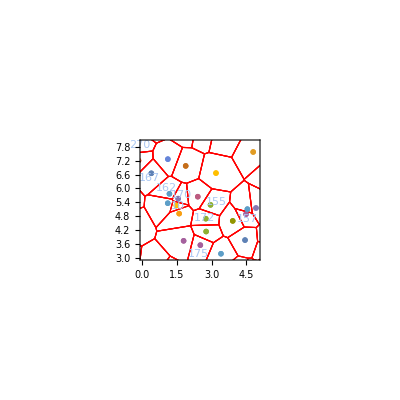

```mathematica
dl=ListPlot[Table[{pointsPBD[[i]]},{i,1,Length[pointsPBD]}],PlotMarkers->Table[i,{i,1,Length[pointsPBD]}]];
Show[HighlightMesh[vm,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dl,PlotRange->{{0,5},{3,8}},Frame->True]
```

```mathematica
cellIndex=Table[Position[Table[RegionMember[polygons[[j]],pointsPBD[[i]]],{j,Length[pointsPBD]}],True][[1,1]],{i,Length[positions]}];
```

```mathematica
cellIndex[[52]]
```

162

```mathematica
box={10,10};
```

```mathematica
anaSigma=Table[deidgGeneral[pointsPBD,polygons[[cellIndex[[a]]]][[1]],pointsPBD[[a]],neighborListRightOrder[a,polygons,cellIndex,pointsPBD],1,1,1,3.75],{a,100}]
```

{0.414438,1.51701,-3.83102,11.796,3.77992,4.27062,-1.13474,2.48177,3.07398,5.29872,0.249022,2.02137,0.204049,2.37104,-0.219835,-1.52573,-1.14017,-0.442818,1.29467,-0.333359,2.82004,-1.34417,-0.0203472,-1.93881,-5.84686,-1.17672,0.111745,-0.957275,-0.230839,-0.457539,0.11212,0.0260952,-0.0608972,2.51061,0.0381583,0.205223,-1.73301,9.18015,-0.0465767,0.300323,-1.69619,1.64299,2.02622,-0.167872,6.36693,0.678886,-1.91026,-0.619377,-0.521887,0.376401,-0.462405,0.193186,0.71848,-0.292519,0.00879741,-0.939558,-0.392375,1.06923,-0.108348,-0.100184,0.774738,2.00354,-0.452003,2.15824,-0.0147299,4.99994,0.180908,0.172619,4.88861,0.0613243,0.00185277,0.906139,0.168182,0.0120057,-0.102513,0.0894378,-0.915544,-0.203121,2.18132,-1.46642,-2.0647,-2.70474,3.96077,-0.663879,0.0500811,0.60987,0.33613,-2.47199,-0.319079,1.46165,-0.612194,-1.22485,0.429459,4.49437,1.26109,-0.234975,0.408981,-2.05003,-0.384829,-1.21748}

```mathematica
ana=AnalyticalCellTest[positions,box,Table[i,{i,100}],1,1,1,3.75]
```

{{0.414438,-0.695522},{1.51701,-4.92765},{-3.83102,35.8464},{11.796,32.0427},{3.77992,17.0014},{4.27062,13.4004},{-1.13474,15.0146},{2.48177,6.54595},{3.07398,-8.77333},{5.29872,18.8731},{0.249022,1.36606},{2.02137,-2.99421},{0.204049,1.38961},{2.37104,12.0984},{-0.219835,6.96657},{-1.52573,10.1179},{-1.14017,4.22689},{-0.442818,4.12654},{1.29467,10.3738},{-0.333359,2.94344},{2.82004,-2.46993},{-1.34417,-1.88294},{-0.0203472,0.00536555},{-1.93881,-2.25806},{-5.84686,-1.6591},{-1.17672,-1.76968},{0.111745,2.12506},{-0.957275,3.94368},{-0.230839,1.03018},{-0.457539,-2.59102},{0.11212,3.83048},{0.0260952,-0.0544629},{-0.0608972,1.80175},{2.51061,22.3696},{0.0381583,1.32462},{0.205223,1.71215},{-1.73301,-7.05575},{9.18015,30.5198},{-0.0465767,0.475532},{0.300323,-5.14029},{-1.69619,-4.94351},{1.64299,-0.692535},{2.02622,5.62846},{-0.167872,0.75322},{6.36693,19.5725},{0.678886,8.77911},{-1.91026,-8.47239},{-0.619377,7.79183},{-0.521887,-0.725348},{0.376401,-5.62439},{-0.462405,7.2679},{0.193186,3.81267},{0.71848,-10.2539},{-0.292519,2.32947},{0.00879741,0.153406},{-0.939558,2.85585},{-0.392375,3.47916},{1.06923,4.75854},{-0.108348,0.833408},{-0.100184,-1.03494},{0.774738,-1.88205},{2.00354,6.14758},{-0.452003,4.38416},{2.15824,-6.29849},{-0.0147299,-0.186899},{4.99994,18.8284},{0.180908,1.25371},{0.172619,0.424847},{4.88861,16.4355},{0.0613243,0.0641348},{0.00185277,0.856495},{0.906139,-1.30612},{0.168182,2.01813},{0.0120057,0.307691},{-0.102513,2.02268},{0.0894378,1.7002},{-0.915544,8.04785},{-0.203121,0.131682},{2.18132,-1.70892},{-1.46642,-4.70047},{-2.0647,-8.86475},{-2.70474,12.8109},{3.96077,11.4706},{-0.663879,5.80837},{0.0500811,-5.9359},{0.60987,-1.93994},{0.33613,4.92995},{-2.47199,-4.42248},{-0.319079,-0.457747},{1.46165,7.09892},{-0.612194,-0.346714},{-1.22485,-0.299512},{0.429459,-2.14347},{4.49437,35.8593},{1.26109,-3.21048},{-0.234975,6.59025},{0.408981,0.263368},{-2.05003,8.64771},{-0.384829,1.53026},{-1.21748,3.95544}}

```mathematica
ana=AnalyticalCell[positions,box,Table[i,{i,100}],1,1,1,3.75]
```

{{-0.341398,1.98431},{-0.0629576,1.05642},{0.16181,0.76407},{0.153366,1.5171},{0.345387,3.07671},{0.091781,0.612013},{0.0567199,0.503033},{-0.0712275,0.400625},{-0.00247664,0.0811969},{-0.0883083,0.423112},{0.0396808,-1.11727},{0.00663071,0.613066},{-0.0607123,0.985616},{-0.0325431,0.539554},{-0.216016,0.495873},{-0.0505331,0.764611},{-0.501553,2.97465},{0.0076135,0.436896},{-0.0198308,1.17598},{-0.0524839,-0.0385699},{0.0241286,0.0857562},{-0.0656225,0.187585},{-0.0168442,0.764996},{0.0349934,0.350368},{0.176526,1.9894},{-0.132378,1.27129},{0.0711,0.742006},{0.00228092,0.0263805},{-0.27568,1.76517},{-0.0694728,0.779138},{0.957796,6.61339},{-0.097214,0.932778},{-0.00206727,0.367753},{0.0321306,0.118102},{0.0220407,0.199074},{-0.0523536,0.319975},{-0.416582,2.21497},{-0.242144,0.818308},{-0.2354,0.99594},{0.0249781,0.346121},{0.0641054,0.454716},{-0.0195372,-0.576584},{0.157581,0.950326},{-0.0709062,1.7479},{-0.270561,1.06393},{-0.0899204,0.681029},{0.209499,0.903165},{-0.0286037,0.300885},{0.0246628,0.755447},{-0.0170891,0.385788},{0.0375572,1.44379},{-0.169819,0.980727},{-0.00880302,0.739679},{-0.312841,2.51756},{0.16721,-0.32941},{0.00926155,0.472151},{-0.17465,0.706371},{-0.0126067,-0.441382},{0.0599747,1.14092},{-0.0217018,1.45375},{-0.00896263,0.306937},{-0.120562,1.23759},{-0.0937552,0.988237},{-0.00624276,0.328993},{0.100771,0.835268},{0.112453,0.607733},{-0.11936,0.910135},{0.0903805,0.607894},{-0.0580876,0.529313},{0.0354162,1.0837},{0.239266,0.16911},{-0.0639308,0.614715},{-0.0621058,0.60471},{-0.0467729,0.838646},{-0.0976451,0.426238},{-0.222479,1.19048},{-0.0243063,-0.0500851},{0.175256,1.15643},{0.280769,1.82502},{0.158636,1.28336},{0.0128294,0.299952},{0.107089,0.723635},{-0.057837,0.538455},{0.540649,3.71284},{0.0544815,0.0672548},{-0.0585991,0.425517},{-0.0158273,0.0936557},{-0.218002,1.33463},{0.00775369,0.185934},{0.091632,-0.305967},{-0.0364502,1.00848},{0.0683225,0.774648},{-0.132289,1.20601},{0.0229526,0.184589},{0.140965,1.06213},{0.17533,2.49704},{0.103711,-0.131631},{-0.0539009,0.43293},{0.08119,0.474209},{0.0263375,0.341727}}

```mathematica
num=numdericalCell[positions,box,0.0001,1,1,1,3.75]
```

{{-0.341398,1.98431},{-0.0629576,1.05642},{0.16181,0.76407},{0.153366,1.5171},{0.345387,3.07672},{0.091781,0.612013},{0.0567199,0.503032},{-0.0712275,0.400625},{-0.00247665,0.081197},{-0.0883083,0.423112},{0.0396808,-1.11727},{0.00663071,0.613067},{-0.0607123,0.985616},{-0.0325431,0.539554},{-0.216016,0.495872},{-0.0505331,0.764611},{-0.501553,2.97465},{0.00761351,0.436896},{-0.0198308,1.17598},{-0.0524839,-0.0385708},{0.0241286,0.0857565},{-0.0656225,0.187585},{-0.0168442,0.764996},{0.0349934,0.350368},{0.176526,1.9894},{-0.132378,1.27129},{0.0711001,0.742006},{0.00228092,0.0263805},{-0.27568,1.76517},{-0.0694728,0.779138},{0.957796,6.61339},{-0.097214,0.932778},{-0.00206727,0.367753},{0.0321306,0.118103},{0.0220407,0.199074},{-0.0523536,0.319975},{-0.416582,2.21497},{-0.242144,0.818308},{-0.2354,0.995941},{0.0249781,0.346122},{0.0641054,0.454716},{-0.0195372,-0.576583},{0.157581,0.950326},{-0.0709062,1.7479},{-0.270561,1.06393},{-0.0899204,0.68103},{0.209499,0.903165},{-0.0286037,0.300885},{0.0246628,0.755447},{-0.0170891,0.385788},{0.0375572,1.44379},{-0.169819,0.980727},{-0.00880302,0.739679},{-0.312841,2.51756},{0.16721,-0.32941},{0.00926156,0.472151},{-0.17465,0.706371},{-0.0126067,-0.441382},{0.0599747,1.14092},{-0.0217018,1.45375},{-0.00896262,0.306937},{-0.120562,1.23759},{-0.0937551,0.988238},{-0.00624276,0.328993},{0.100771,0.835268},{0.112453,0.607734},{-0.11936,0.910135},{0.0903805,0.607894},{-0.0580876,0.529313},{0.0354163,1.0837},{0.239266,0.16911},{-0.0639308,0.614715},{-0.0621058,0.60471},{-0.0467729,0.838646},{-0.0976451,0.426238},{-0.222479,1.19048},{-0.0243063,-0.0500848},{0.175256,1.15643},{0.280769,1.82502},{0.158636,1.28336},{0.0128294,0.299952},{0.107089,0.723635},{-0.057837,0.538455},{0.540649,3.71284},{0.0544815,0.0672551},{-0.0585991,0.425517},{-0.0158273,0.0936557},{-0.218002,1.33463},{0.00775369,0.185934},{0.091632,-0.305968},{-0.0364502,1.00848},{0.0683225,0.774648},{-0.132289,1.20601},{0.0229526,0.184589},{0.140965,1.06213},{0.17533,2.49704},{0.103711,-0.131631},{-0.0539009,0.43293},{0.08119,0.47421},{0.0263375,0.341727}}

```mathematica
Normal[data[[10,1]]]
```

{0.414438,1.51701,-3.83102,11.796,3.77992,4.27062,-1.13474,2.48177,3.07398,5.29872,0.249022,2.02137,0.204049,2.37104,-0.219835,-1.52573,-1.14017,-0.442818,1.29467,-0.333359,2.82004,-1.34417,-0.0203472,-1.93881,-5.84686,-1.17672,0.111745,-0.957275,-0.230839,-0.457539,0.11212,0.0260952,-0.0608972,2.51061,0.0381583,0.205223,-1.73301,9.18015,-0.0465767,0.300323,-1.69619,1.64299,2.02622,-0.167872,6.36693,0.678886,-1.91026,-0.619377,-0.521887,0.376401,-0.462405,0.193186,0.71848,-0.292519,0.00879741,-0.939558,-0.392375,1.06923,-0.108348,-0.100184,0.774738,2.00354,-0.452003,2.15824,-0.0147299,4.99994,0.180908,0.172619,4.88861,0.0613243,0.00185277,0.906139,0.168182,0.0120057,-0.102513,0.0894378,-0.915544,-0.203121,2.18132,-1.46642,-2.0647,-2.70474,3.96077,-0.663879,0.0500811,0.60987,0.33613,-2.47199,-0.319079,1.46165,-0.612194,-1.22485,0.429459,4.49437,1.26109,-0.234975,0.408981,-2.05003,-0.384829,-1.21748}

```mathematica
Max[Abs[Table[({data[[10,10]][[i]],data[[4,10]][[i]]}-num[[i]])/num[[i]],{i,100}]]]
```

0.0000234327

```mathematica
Max[Abs[Table[({data[[10,10]][[i]],data[[4,10]][[i]]}-ana[[i]])/ana[[i]],{i,100}]]]
```

2.36031×10^-11

{{0.414438,-0.695522},{1.51701,-4.92765},{-3.83102,35.8464},{11.796,32.0427},{3.77992,17.0014},{4.27062,13.4004},{-1.13474,15.0146},{2.48177,6.54595},{3.07398,-8.77333},{5.29872,18.8731},{0.249022,1.36606},{2.02137,-2.99421},{0.204049,1.38961},{2.37104,12.0984},{-0.219835,6.96657},{-1.52573,10.1179},{-1.14017,4.22689},{-0.442818,4.12654},{1.29467,10.3738},{-0.333359,2.94344},{2.82004,-2.46993},{-1.34417,-1.88294},{-0.0203472,0.00536555},{-1.93881,-2.25806},{-5.84686,-1.6591},{-1.17672,-1.76968},{0.111745,2.12506},{-0.957275,3.94368},{-0.230839,1.03018},{-0.457539,-2.59102},{0.11212,3.83048},{0.0260952,-0.0544629},{-0.0608972,1.80175},{2.51061,22.3696},{0.0381583,1.32462},{0.205223,1.71215},{-1.73301,-7.05575},{9.18015,30.5198},{-0.0465767,0.475532},{0.300323,-5.14029},{-1.69619,-4.94351},{1.64299,-0.692535},{2.02622,5.62846},{-0.167872,0.75322},{6.36693,19.5725},{0.678886,8.77911},{-1.91026,-8.47239},{-0.619377,7.79183},{-0.521887,-0.725348},{0.376401,-5.62439},{-0.462405,7.2679},{0.193186,3.81267},{0.71848,-10.2539},{-0.292519,2.32947},{0.00879741,0.153406},{-0.939558,2.85585},{-0.392375,3.47916},{1.06923,4.75854},{-0.108348,0.833408},{-0.100184,-1.03494},{0.774738,-1.88205},{2.00354,6.14758},{-0.452003,4.38416},{2.15824,-6.29849},{-0.0147299,-0.186899},{4.99994,18.8284},{0.180908,1.25371},{0.172619,0.424847},{4.88861,16.4355},{0.0613243,0.0641348},{0.00185277,0.856495},{0.906139,-1.30612},{0.168182,2.01813},{0.0120057,0.307691},{-0.102513,2.02268},{0.0894378,1.7002},{-0.915544,8.04785},{-0.203121,0.131682},{2.18132,-1.70892},{-1.46642,-4.70047},{-2.0647,-8.86475},{-2.70474,12.8109},{3.96077,11.4706},{-0.663879,5.80837},{0.0500811,-5.9359},{0.60987,-1.93994},{0.33613,4.92995},{-2.47199,-4.42248},{-0.319079,-0.457747},{1.46165,7.09892},{-0.612194,-0.346714},{-1.22485,-0.299512},{0.429459,-2.14347},{4.49437,35.8593},{1.26109,-3.21048},{-0.234975,6.59025},{0.408981,0.263368},{-2.05003,8.64771},{-0.384829,1.53026},{-1.21748,3.95544}}

```mathematica
num
```

{{-0.414438,-0.695521},{-1.51701,-4.92765},{3.83102,35.8464},{-11.796,32.0427},{-3.77992,17.0014},{-4.27062,13.4004},{1.13474,15.0146},{-2.48177,6.54596},{-3.07398,-8.77334},{-5.29872,18.8731},{-0.249022,1.36606},{-2.02137,-2.99421},{-0.204049,1.38961},{-2.37104,12.0984},{0.219835,6.96657},{1.52573,10.1179},{1.14017,4.22689},{0.442818,4.12654},{-1.29467,10.3738},{0.333359,2.94344},{-2.82004,-2.46994},{1.34417,-1.88294},{0.0203472,0.00536548},{1.93881,-2.25806},{5.84686,-1.6591},{1.17672,-1.76968},{-0.111745,2.12506},{0.957275,3.94368},{0.230839,1.03019},{0.457539,-2.59102},{-0.11212,3.83048},{-0.0260951,-0.0544629},{0.0608972,1.80175},{-2.51061,22.3696},{-0.0381583,1.32462},{-0.205223,1.71215},{1.73301,-7.05576},{-9.18015,30.5198},{0.0465767,0.475529},{-0.300323,-5.14029},{1.69619,-4.94351},{-1.64299,-0.692533},{-2.02622,5.62846},{0.167872,0.753221},{-6.36693,19.5725},{-0.678886,8.7791},{1.91026,-8.47239},{0.619377,7.79183},{0.521887,-0.725348},{-0.376401,-5.62438},{0.462406,7.2679},{-0.193186,3.81267},{-0.71848,-10.2539},{0.292519,2.32947},{-0.00879741,0.153406},{0.939558,2.85585},{0.392375,3.47916},{-1.06923,4.75854},{0.108348,0.833408},{0.100184,-1.03495},{-0.774738,-1.88205},{-2.00354,6.14758},{0.452003,4.38416},{-2.15824,-6.29849},{0.0147299,-0.186899},{-4.99994,18.8284},{-0.180908,1.25371},{-0.172619,0.424846},{-4.88861,16.4355},{-0.0613243,0.0641348},{-0.00185277,0.856495},{-0.906139,-1.30612},{-0.168182,2.01813},{-0.0120057,0.307691},{0.102513,2.02268},{-0.0894378,1.7002},{0.915544,8.04785},{0.203121,0.131682},{-2.18132,-1.70892},{1.46642,-4.70047},{2.0647,-8.86475},{2.70474,12.8109},{-3.96077,11.4706},{0.663879,5.80837},{-0.0500812,-5.9359},{-0.60987,-1.93993},{-0.33613,4.92995},{2.47199,-4.42248},{0.319079,-0.457747},{-1.46165,7.09893},{0.612194,-0.346713},{1.22485,-0.299512},{-0.429459,-2.14347},{-4.49437,35.8593},{-1.26109,-3.21048},{0.234975,6.59025},{-0.408981,0.263369},{2.05003,8.64771},{0.384829,1.53026},{1.21748,3.95544}}

```mathematica
pre=Import["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/testData/preliminary_N900_p3.800_T0.010_time10000.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/d2Edgammadgamma→NumericArray[…],/energy→NumericArray[…],/sigma→NumericArray[…]|>

```mathematica
pre[[1,100,1]]
```

243.969

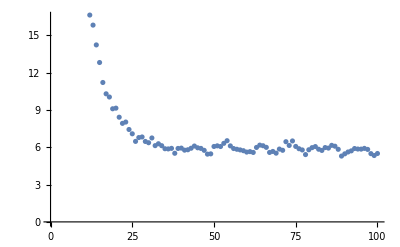

```mathematica
ListPlot[Table[pre[[3,i,1]],{i,100}]]
```

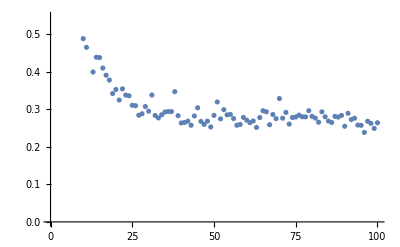

```mathematica
ListPlot[Table[pre[[2,i,1]]/900,{i,100}]]
```

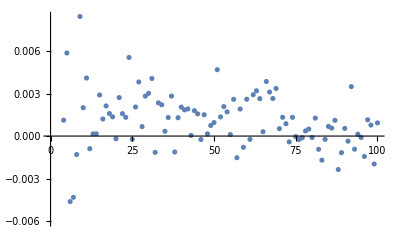

```mathematica
ListPlot[Table[pre[[4,i,1]],{i,100}]]
```